```mathematica
pm = Import["C:\\Users\\Nikita\\Desktop\\TPM\\N_body_TPM\\Sources\\source-vs\\pm_m.txt","Table"];
```

```mathematica
PM={};
For[i=1 , i<Length[pm],i++,
AppendTo[PM, {pm[[i,1]], pm[[i,2]]}];
]
```

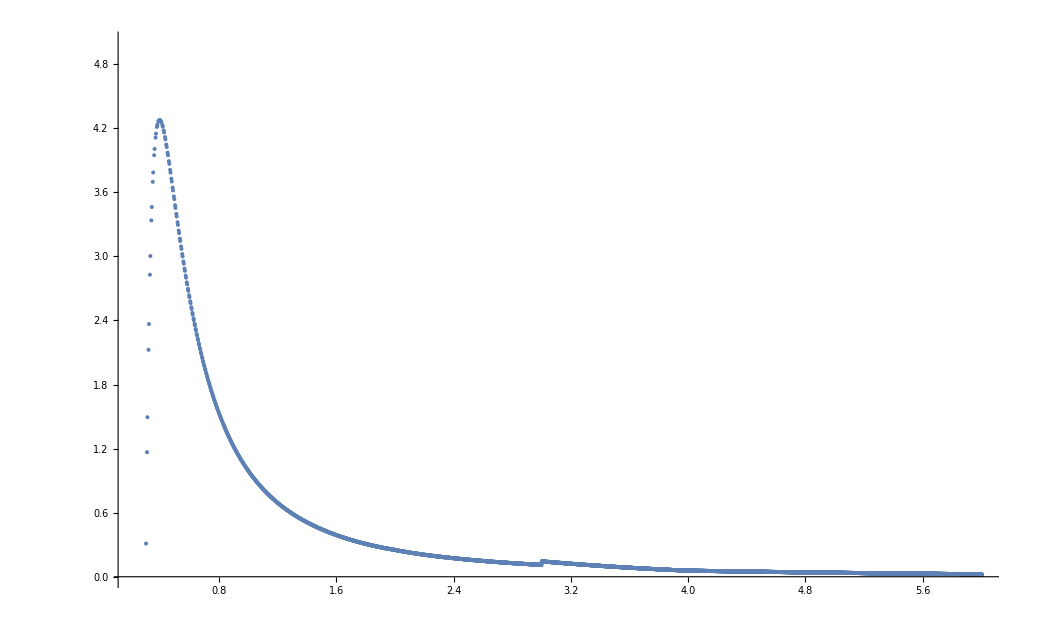

```mathematica
ListPlot[PM , PlotRange->5]
```

```mathematica
dir = Import["C:\\Users\\Nikita\\Desktop\\TPM\\N_body_TPM\\Sources\\source-vs\\dir_m.txt","Table"];
```

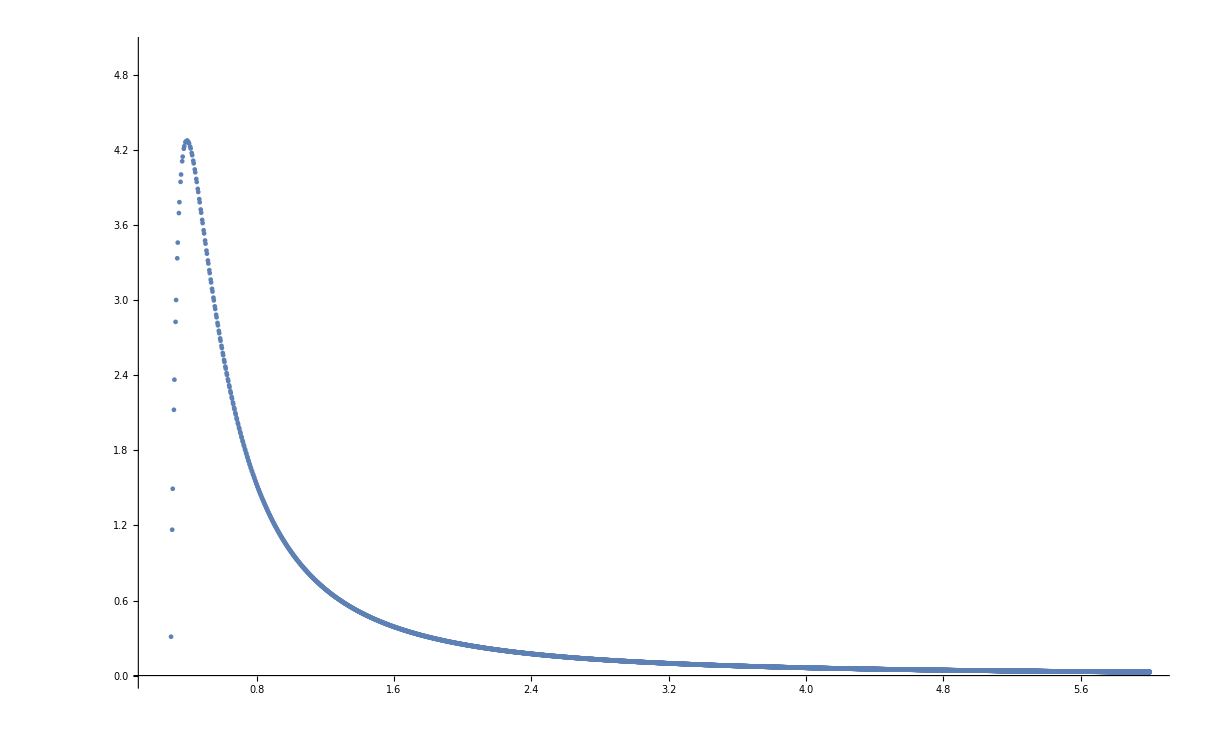

```mathematica
ListPlot[dir, PlotRange->5]
```

```mathematica
dif = {};
For[i=1 , i≤ Length[dir], i++,
AppendTo[dif, {dir[[i,1]], pm[[i, 2]]- dir[[i,2]]}];
]
```

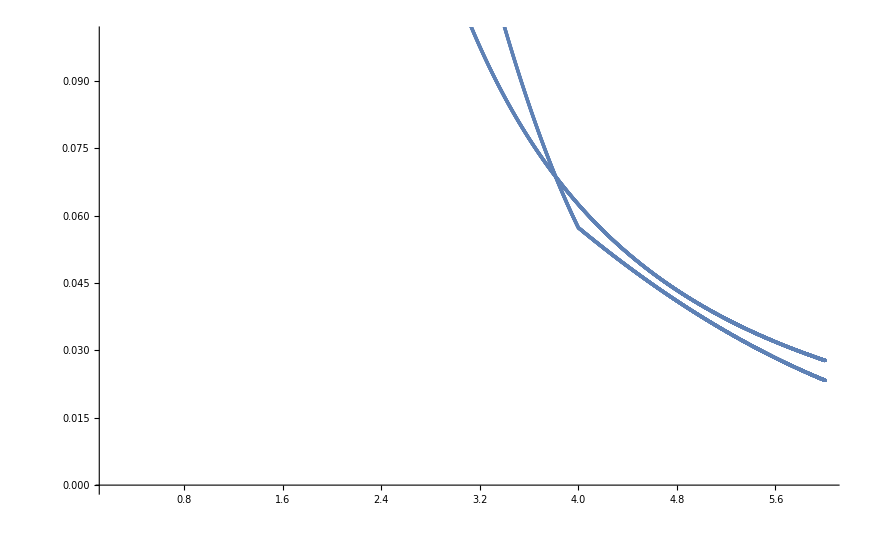

```mathematica
Show[%4, %8, PlotRange->{0,0.1}]
```

```mathematica
dif
```

{{6,-0.00444},{6,-0.00444},{6,-0.00444},{6,-0.00444},{6,-0.0044399},{5.99999,-0.00444},{5.99999,-0.00444},{5.99999,-0.0044399},{5.99998,-0.00444},{5.99998,-0.00444},{5.99998,-0.0044399},{5.99997,-0.00444},{5.99996,-0.0044399},{5.99996,-0.0044399},{5.99995,-0.0044399},6396,{5.56447,-0.0034934},{5.56514,-0.0034948},{5.5658,-0.0034962},{5.56646,-0.0034976},{5.56712,-0.003499},{5.56778,-0.0035005},{5.56844,-0.0035019},{5.5691,-0.0035034},{5.56976,-0.0035049},{5.57042,-0.0035063},{5.57108,-0.0035078},{5.57173,-0.0035092},{5.57239,-0.0035106},{5.57305,-0.003512}}
 |  |  |  |

```mathematica
Fit
```

Fit

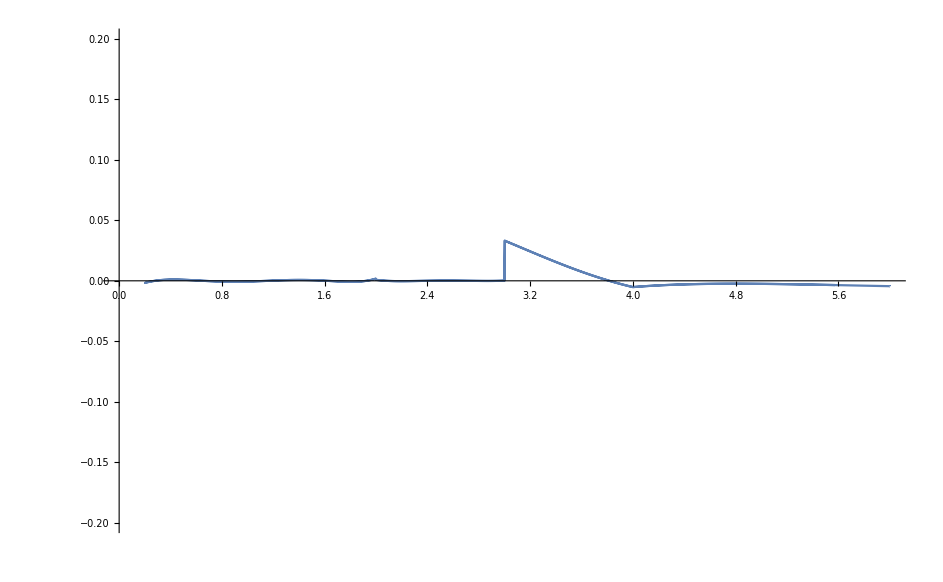

```mathematica
ListLinePlot[dif , PlotRange->{-0.2,0.2}]
```

```mathematica
data1 ={};
For[i=1 , i<Length[dif],i++,
If[dif[[i,1]]≤3 && dif[[i,1]]≥ 2 , AppendTo[data1, { dif[[i,1]] , dif[[i,2]]}] , ]
]
```

```mathematica
Length[data1]
```

660

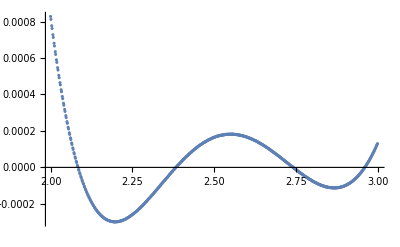

```mathematica
ListPlot[data1]
```

```mathematica
data2={};
For[i=1 , i<Length[dif],i++,
If[dif[[i,1]]≤2, AppendTo[data2, { dif[[i,1]] , dif[[i,2]]}] , ]
]
```

```mathematica
line1 = Fit[data1 , {1, x , x^2}, x]
```

0.000245883-0.000187905 x+0.0000357554 x^2

```mathematica
line2 = Fit[data2 , {1, x , x^2, x^3, x^4}, x]
```

-0.000118078+0.000847916 x-0.00169914 x^2+0.0012518 x^3-0.000304341 x^4

0.0565894+0.012286 x+0.135934 x^2-0.0843915 x^3

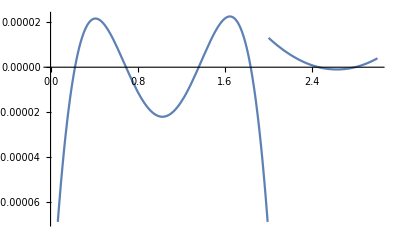

```mathematica
0.05658944320060551+0.012285964611120852 x+0.1359338468325688 x^2-0.08439149362240658 x^3

cur[x_]= Plot[Piecewise[{{line1,2<x≤3},{line2,x<2}}],{x,0,3}]
```

```mathematica
Show[%30, %47]
```

Show::gcomb: Could not combine the graphics objects in Show[%30,%47].

Show[%30,%47]

```mathematica
sh = Import["C:\\Users\\Nikita\\Desktop\\TPM\\N_body_TPM\\Sources\\source-vs\\sh_m.txt","Table"];
```

```mathematica
er={};
For[i=1 , i≤Length[sh], i++,
AppendTo[er, {sh[[i,2]], sh[[i,3]]}];
]
```

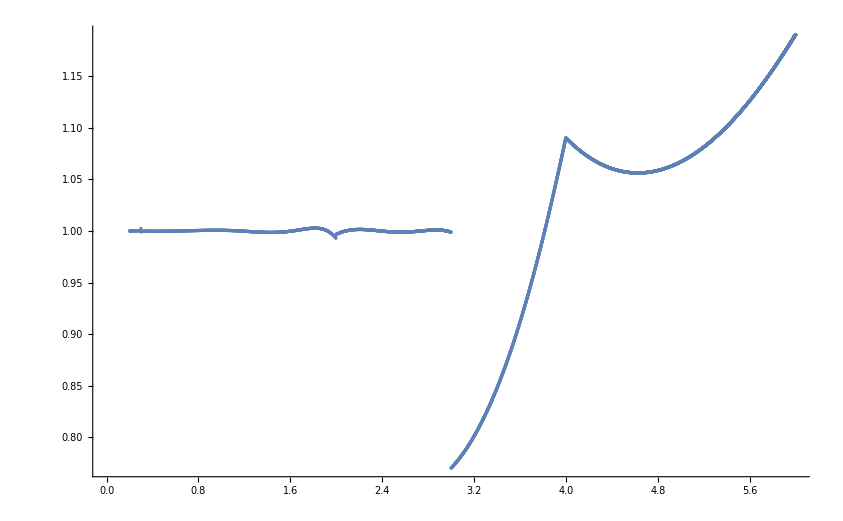

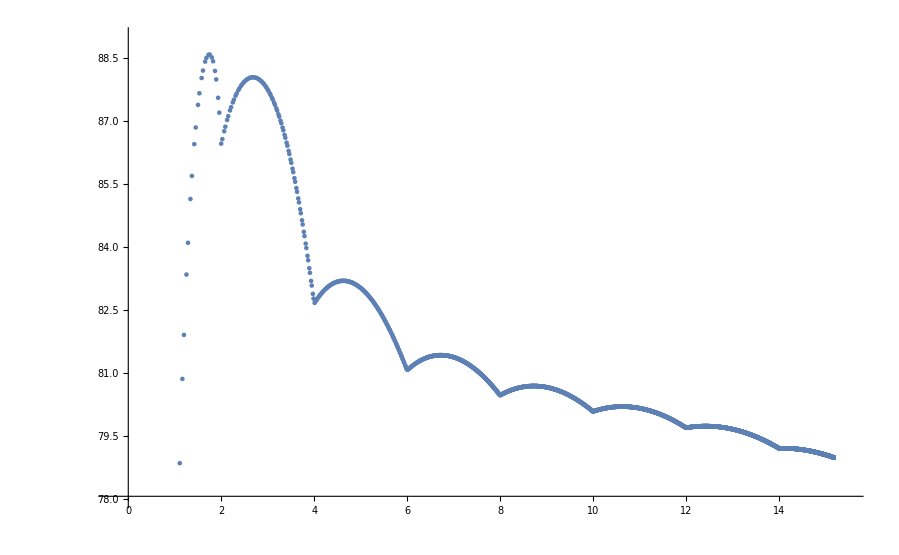

```mathematica
ListPlot[er]
```

```mathematica
er
```

{{6,1.19025},{6,1.19025},{6,1.19025},{6,1.19025},{6,1.19025},{5.99999,1.19025},{5.99999,1.19025},{5.99999,1.19025},{5.99998,1.19025},{5.99998,1.19025},{5.99998,1.19025},{5.99997,1.19025},{5.99996,1.19024},{5.99996,1.19024},{5.99995,1.19024},{5.99995,1.19024},{5.99994,1.19024},{5.99993,1.19024},{5.99992,1.19024},{5.99991,1.19024},{5.99991,1.19023},{5.9999,1.19023},{5.99989,1.19023},{5.99988,1.19023},6377,{5.55782,1.1204},{5.55848,1.12049},{5.55915,1.12058},{5.55982,1.12066},{5.56049,1.12075},{5.56115,1.12084},{5.56182,1.12093},{5.56248,1.12102},{5.56315,1.12111},{5.56381,1.1212},{5.56447,1.12128},{5.56514,1.12137},{5.5658,1.12146},{5.56646,1.12155},{5.56712,1.12164},{5.56778,1.12173},{5.56844,1.12182},{5.5691,1.1219},{5.56976,1.12199},{5.57042,1.12208},{5.57108,1.12217},{5.57173,1.12226},{5.57239,1.12235},{5.57305,1.12243}}
 |  |  |  |

```mathematica
sh
```

{{1,6,1.19025,0.000145295},{2,6,1.19025,0.000290591},{3,6,1.19025,0.000435886},{4,6,1.19025,0.000581182},{5,6,1.19025,0.000726477},{6,5.99999,1.19025,0.000871773},{7,5.99999,1.19025,0.00101707},{8,5.99999,1.19025,0.00116237},{9,5.99998,1.19025,0.00130766},{10,5.99998,1.19025,0.00145296},{11,5.99998,1.19025,0.00159826},{12,5.99997,1.19025,0.00174355},{13,5.99996,1.19024,0.00188885},6399,{6413,5.56514,1.12137,0.212713},{6414,5.5658,1.12146,0.212534},{6415,5.56646,1.12155,0.212355},{6416,5.56712,1.12164,0.212175},{6417,5.56778,1.12173,0.211996},{6418,5.56844,1.12182,0.211817},{6419,5.5691,1.1219,0.211638},{6420,5.56976,1.12199,0.21146},{6421,5.57042,1.12208,0.211281},{6422,5.57108,1.12217,0.211102},{6423,5.57173,1.12226,0.210923},{6424,5.57239,1.12235,0.210745},{6425,5.57305,1.12243,0.210566}}
 |  |  |  |

-Graphics-

```mathematica
f={};
For[i=1 , i≤Length[sh],i++,
AppendTo[f , {sh[[i,2]] , sh[[i,4]]}];
]
```

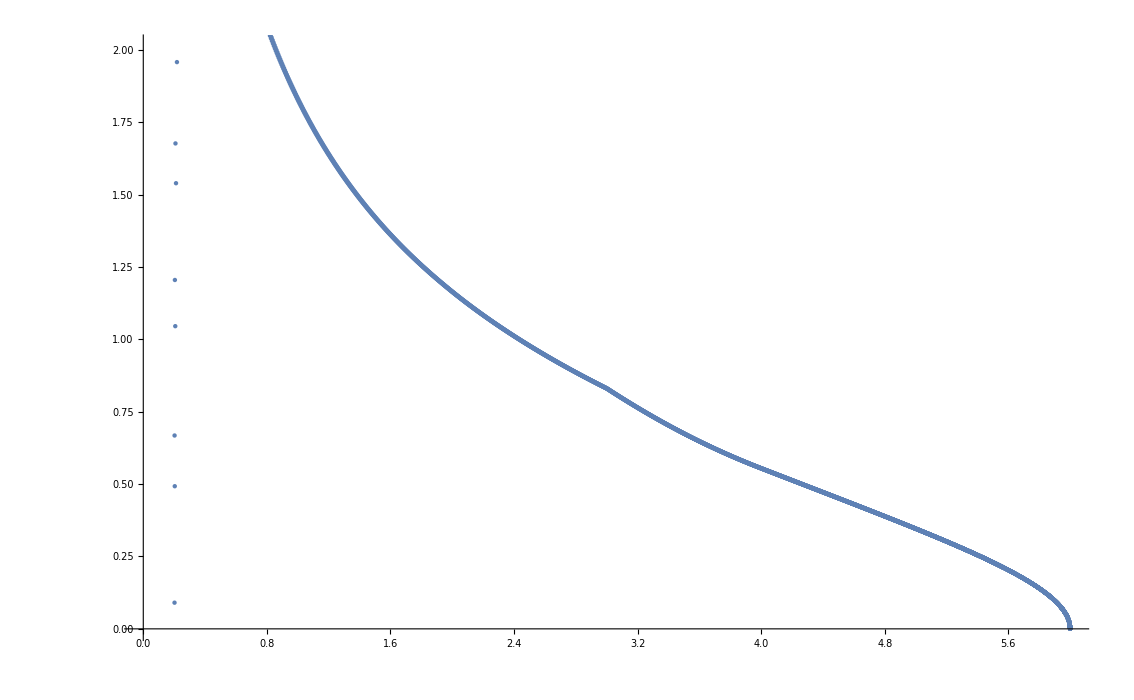

```mathematica
ListPlot[f]
```